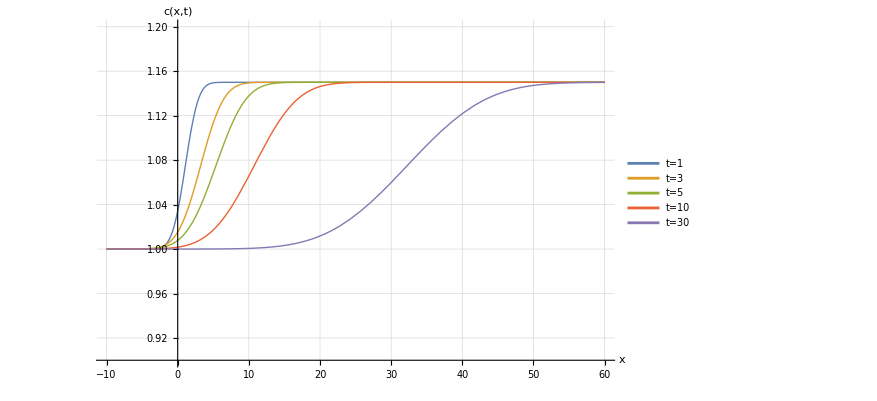

```mathematica
cplus=1.15;     
cminus=1;   
v=1;            

eplus[x_,t_]:=Exp[(cplus*(cplus*t-2*x))/(4*v)]*(1+Erf[(x-cplus*t)/(2*Sqrt[v*t])]);
eminus[x_,t_]:=Exp[(cminus*(cminus*t-2*x))/(4*v)]*(1-Erf[(x-cminus*t)/(2*Sqrt[v*t])]);

c[x_,t_]:=(cplus*eplus[x,t]+cminus*eminus[x,t])/(eplus[x,t]+eminus[x,t]);

data=Plot[Evaluate[Table[c[x,t],{t,{1,3, 5,10,30}}]],{x,-10,60},PlotRange->{0.9,1.2},AxesLabel->{"x","c(x,t)"},PlotLegends->Placed[{"t=1","t=3","t=5","t=10","t=30"},Right],PlotStyle->{Thick,Thick,Thick,Thick,Thick},GridLines->Automatic,ImageSize->650,LabelStyle->{FontFamily->"Arial",FontSize->12}]
```

```mathematica
Export["D:\Study\Волновые процессы\1.jpg",data];
```

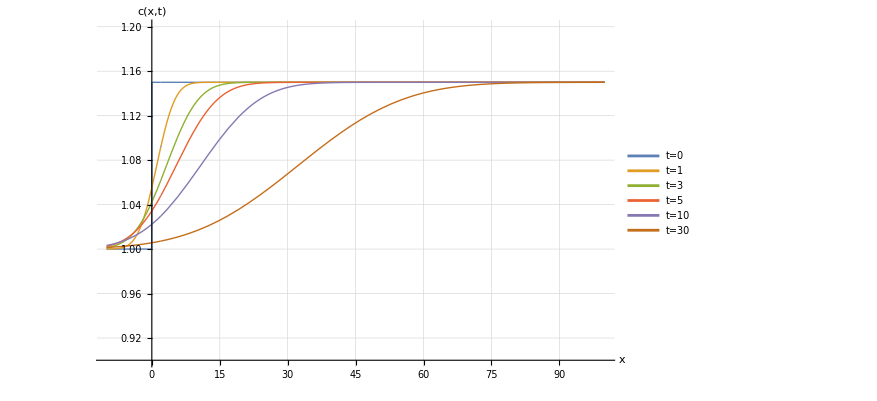

```mathematica
cplus=1.15;
cminus=1;
v=5;

eplus[x_,t_]:=If[t==0,2*Exp[-(cplus*x)/(2*v)]*UnitStep[x],Exp[(cplus*(cplus*t-2*x))/(4*v)]*(1+Erf[(x-cplus*t)/(2*Sqrt[v*t])])];

eminus[x_,t_]:=If[t==0,2*Exp[-(cminus*(-x))/(2*v)]*UnitStep[-x],Exp[(cminus*(cminus*t-2*x))/(4*v)]*(1-Erf[(x-cminus*t)/(2*Sqrt[v*t])])];

c[x_,t_]:=(cplus*eplus[x,t]+cminus*eminus[x,t])/(eplus[x,t]+eminus[x,t]);

data=Plot[Evaluate[Table[c[x,t],{t,{0,1,3,5,10,30}}]],{x,-10,100},PlotRange->{0.9,1.2},AxesLabel->{"x","c(x,t)"},PlotLegends->Placed[{"t=0","t=1","t=3","t=5","t=10","t=30"},Right],PlotStyle->Table[Thick,6],GridLines->Automatic,ImageSize->650,LabelStyle->{FontFamily->"Arial",FontSize->12},Exclusions->{{x==2}},ExclusionsStyle->Directive[Gray,Dashed]]
```

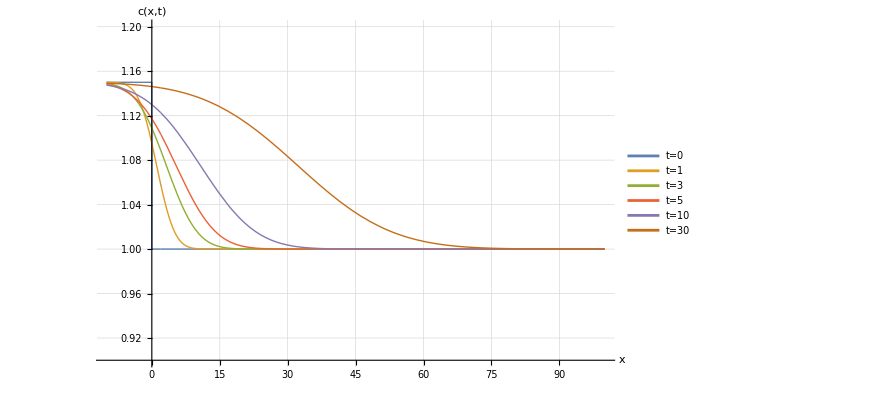

```mathematica
Animate[Plot[c[x,t],{x,-10,40},PlotRange->{0.9,1.2},AxesLabel->{"x","c(x,t)"},GridLines->Automatic],{t,0,30}]
```